```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/gabrielefranciolini/Desktop

```mathematica
lp=100;
rp=20;
AT2=AbsoluteThickness[2];
AT3=AbsoluteThickness[3];
```

### Preliminary commands

```mathematica
SetOptions[EvaluationNotebook[],"ShowGroupOpener"->True];
```

```mathematica
logsample[a_,b_,n_]:=Exp[Range[Log[a//N],Log[b],Log[b/a]/n]]
```

```mathematica
fontLaTeXstyle={"CMU Serif","Latin Modern Roman"}[[1]];
(*CubaDirectory="/Users/gabrielefranciolini/Dropbox/Macbook/Mathematica/Packages/";*)
(*Install[ToString[CubaDirectory<>"Cuba-4.2/Divonne"]];
Install[ToString[CubaDirectory<>"Cuba-4.2/Suave"]];
Install[ToString[CubaDirectory<>"Cuba-4.2/Vegas"]];*)
```

#### Automatic save of the notebook

```mathematica
(*memory:=Print["Memory in use: ",MemoryInUse[]/1024.^2," Mb"]*)
```

This command saves automatically the notebook every 3 minutes, since I got sick of losing my modifications because Mathematica crashed and I haven’t saved in a while:

```mathematica
(*startsaveTask:=Block[{saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],3*60]},StartScheduledTask[saveTask]]*)
```

```mathematica
(*startsaveTask*)
```

To block this automatic saving task:

```mathematica
(*stopsaveTask:=RemoveScheduledTask[CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],3*60]]*)
```

#### MaTeX

To install MaTeX, a cool add-on to have LATEX labels, run this command after having downloaded the package from here:
https://github.com/szhorvat/MaTeX/releases

```mathematica
(*PacletInstall["~/Desktop/MaTeX-1.7.8.paclet"]*)
```

```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
MaTeX["\\lambda_\\text{LISA}",Magnification->2,ContentPadding->False]
```

-Graphics-

```mathematica
NiceFormat[x_]:=If[.01≤x<1000,NumberForm[x,3],ScientificForm[N[x],3,NumberFormat->(Row[{#1," ·10^",#3}]&)]]
```

```mathematica
Clear@TexFormat
TexFormat[x_]:=ToString[If[.001≤x<1000,NumberForm[x,3],
ScientificForm[1.*x,3]//TeXForm]]
```

```mathematica
TexFormat[π 10^9]
```

3.14\times 10^9

```mathematica
Block[{
opt={BaseStyle->{FontFamily->fontLaTeXstyle,FontSize->24}
(*LabelStyle->{FontColor->Black}*)},
opt2D={Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->AbsoluteThickness[1.2],ImageSize->900},
optList={Joined->True},
optAll},
optAll=Join[opt,opt2D];
SetOptions[Plot,optAll];
SetOptions[ListPlot,optAll];
SetOptions[LogPlot,optAll];
SetOptions[ListLogPlot,optAll];
SetOptions[LogLinearPlot,optAll];
SetOptions[ListLogLinearPlot,optAll];
SetOptions[LogLogPlot,optAll];
SetOptions[ListLogLogPlot,optAll];
SetOptions[ContourPlot,optAll];
SetOptions[ListContourPlot,optAll];
SetOptions[Histogram,optAll];
SetOptions[SmoothHistogram,optAll];
]
```

White shadow inside Legends:

```mathematica
Clear@frame
frame[legend_]:=Framed[legend,FrameStyle->Transparent,RoundingRadius->10,Background->Opacity[.6,White]]
```

#### User-defined colours

These commands show the colour you compose :

```mathematica
colRed0 = RGBColor[0.85, 0.05, 0.12];colRed1 = RGBColor[0.92, 0.1, 0.05];colRed2 = RGBColor[0.95, 0.35, 0.05];colYellow1 =  RGBColor[1., 0.82, 0.];
Row[{Graphics[{colRed0, Disk[]}, ImageSize -> 50],Graphics[{colRed1, Disk[]}, ImageSize -> 50],Graphics[{colRed2, Disk[]}, ImageSize -> 50],Graphics[{colYellow1, Disk[]}, ImageSize -> 50]}]
colBlue1 = RGBColor[0.0, 0., 0.4]; colBlue2 =  RGBColor[0.1, 0.3, 0.9];colBlue3 =  RGBColor[0.15, 0.4, 0.75]; colBlue4 = RGBColor[0.3, 0.8, 0.93];
Row[{Graphics[{colBlue1, Disk[]}, ImageSize -> 50], Graphics[{colBlue2, Disk[]}, ImageSize -> 50], Graphics[{colBlue3, Disk[]}, ImageSize -> 50],Graphics[{colBlue4, Disk[]}, ImageSize -> 50]}]
colGreen0=RGBColor[0.0,0.15,0.05];colGreen1 = RGBColor[0.0, 0.35, 0.1]; colGreen2=RGBColor[0.1, 0.65, 0.2]; colGreen3 = RGBColor[0.3, 0.85, 0.5];
Row[{Graphics[{colGreen0, Disk[]}, ImageSize -> 50],Graphics[{colGreen1, Disk[]}, ImageSize -> 50], Graphics[{colGreen2, Disk[]}, ImageSize -> 50],Graphics[{colGreen3, Disk[]}, ImageSize -> 50]}]
colBrown1=RGBColor[0.3,0.18,0.12];colBrown2= RGBColor[0.5, 0.3, 0.20];
Row[{Graphics[{colBrown1, Disk[]}, ImageSize -> 50],Graphics[{colBrown2, Disk[]}, ImageSize -> 50]}]
colViolet1=RGBColor[0.4,0.18,0.42];colViolet2= RGBColor[0.5, 0.3, 0.70];
Row[{Graphics[{colViolet1, Disk[]}, ImageSize -> 50],Graphics[{colViolet2, Disk[]}, ImageSize -> 50]}]
```

-Graphics--Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

```mathematica
bosonsCol=RGBColor[0.15,0.2,0.6]
gluonsCol=RGBColor[0.5,0.1,0.7]
lightQCol=RGBColor[0.9,0.1,0.]
heavyQCol=RGBColor[0.1,0.5,0.1]
leptonCol=RGBColor[1.,.6,0.1]
```

RGBColor[0.15, 0.2, 0.6]

RGBColor[0.5, 0.1, 0.7]

RGBColor[0.9, 0.1, 0.]

RGBColor[0.1, 0.5, 0.1]

RGBColor[1., 0.6, 0.1]

```mathematica
AT2=AbsoluteThickness[2];
AD=Dashed;
FS=500;
```

#### Customised ticks for plots

Length for the ticks:

```mathematica
tick2=0.007;
tick1=1.8tick2;
tickmax=100;
```

```mathematica
llab=Table[tick[n,m],{m,1,9},{n,-40,40}];
llabLog=Flatten[llab]/.tick[n_,m_]->If[m==1,{Log[10.,m*10^n],DisplayForm[m*SuperscriptBox[10,n]]},{Log[10.,m*10^n],""}];
ltickLog=Flatten[Table[{Log[10.,m*10^n],""},{m,1,9},{n,-tickmax,tickmax}],1];
```

```mathematica
llabLin=Flatten[llab]/.tick[n_,m_]->If[m==1,{m*10^n,DisplayForm[m*SuperscriptBox[10,n]],{tick1,0}},{m*10^n,"",{tick2,0}}];
ltickLin=Flatten[llab]/.tick[n_,m_]->If[m==1,{m*10^n,"",{tick1,0}},{m*10^n,"",{tick2,0}}];
```

```mathematica
llabInt=Table[tick[n],{n,-tickmax,tickmax}];
```

```mathematica
(*llabLin2=Flatten[llabInt]/.tick[n_]->If[Mod[n,2]==0,{10^n,DisplayForm[SuperscriptBox[10,n]]},{10^n,""}];
ltickLin2=Table[{10^n,""},{n,-140,140}];*)
```

```mathematica
llabLin1=Flatten[llabInt]/.tick[n_]->If[Mod[n,1]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin1=Flatten[llabInt]/.tick[n_]->If[Mod[n,1]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];
```

```mathematica
llabLin2=Flatten[llabInt]/.tick[n_]->If[Mod[n,2]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin2=Flatten[llabInt]/.tick[n_]->If[Mod[n,2]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];
```

```mathematica
llabLin3=Flatten[llabInt]/.tick[n_]->If[Mod[n,3]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin3=Flatten[llabInt]/.tick[n_]->If[Mod[n,3]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];
```

```mathematica
llabLin4=Flatten[llabInt]/.tick[n_]->If[Mod[n,4]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin4=Flatten[llabInt]/.tick[n_]->If[Mod[n,4]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];

llabLin10=Flatten[llabInt]/.tick[n_]->If[Mod[n,10]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin10=Flatten[llabInt]/.tick[n_]->If[Mod[n,10]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];

llabLin20=Flatten[llabInt]/.tick[n_]->If[Mod[n,20]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin20=Flatten[llabInt]/.tick[n_]->If[Mod[n,20]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];
```

#### Set options for plots

```mathematica
AT2=AbsoluteThickness[2];
```

```mathematica
SetOptions[Plot,PlotRange->All,ImageSize->500,PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}}];
SetOptions[ListPlot,ImageSize->500,Joined->True,InterpolationOrder->2,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All];
SetOptions[LogPlot,ImageSize->500];
SetOptions[LogLogPlot,ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All,FrameTicks->{{llabLin,ltickLin},{llabLin,ltickLin}}];
SetOptions[LogLinearPlot,ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All,FrameTicks->{Automatic,{llabLin,ltickLin}}];
SetOptions[ListLinePlot,ImageSize->500];
SetOptions[ListPlot3D,ImageSize->500,ColorFunction->"BlueGreenYellow"];
SetOptions[ListContourPlot,ColorFunction->"BlueGreenYellow",ImageSize->500];
SetOptions[ListLogLinearPlot,FrameTicks->{Automatic,{llabLin,ltickLin}},Joined->True,InterpolationOrder->2,ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All];
SetOptions[ListLogLogPlot,Joined->True,InterpolationOrder->2,ImageSize->500,
PlotStyle->{{colBlue1,AT2,Dashed},{colRed0,AT2,Dashed},{colGreen0,AT2,Dashed},{colRed2,AT2,Dashed},{colBlue4,AT2,Dashed}},PlotRange->All];
SetOptions[ListLogPlot,FrameTicks->{{llabLin,ltickLin},Automatic},Joined->True,InterpolationOrder->2,ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All];
SetOptions[LogPlot,FrameTicks->{{llabLin,ltickLin},Automatic},ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All];
SetOptions[ListLogLogPlot,FrameTicks->{{llabLin,ltickLin},{llabLin,ltickLin}},Joined->True,InterpolationOrder->2,ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All];
```

```mathematica
(*Epilog->{ddx=0.54;ddy=0.45;
{
{colBlue1,AT2,Line[{Scaled[{.13+ddx,.12+ddy}],Scaled[{.15+ddx,.12+ddy}],Scaled[{.16+ddx,.12+ddy}]}]}},
Text[MaTeX["\\alpha=0.5",Magnification->1.7],Scaled[{.18+ddx,.07+ddy }],{1,0}],
{{colRed0,AT2,Dashed,Line[{Scaled[{.13+ddx,.12+.1+ddy}],Scaled[{.15+ddx,.12+.1+ddy}],Scaled[{.16+ddx,.12+.1+ddy}]}]}},
Text[MaTeX["\\alpha=1",Magnification->1.7],Scaled[{.18+ddx,.07+.1+ddy }],{1,0}],
{{colGreen1,AT2,Dashed,Line[{Scaled[{.13+ddx,.12+.2+ddy}],Scaled[{.15+ddx,.12+.2+ddy}],Scaled[{.16+ddx,.12+.2+ddy}]}]}},
Text[MaTeX["\\alpha=2",Magnification->1.7],Scaled[{.18+ddx,.07+.2+ddy }],{1,0}],
{{colRed2,AT2,DotDashed,Line[{Scaled[{.13+ddx,.12+.3+ddy}],Scaled[{.15+ddx,.12+.3+ddy}],Scaled[{.16+ddx,.12+.3+ddy}]}]}},
Text[MaTeX["\\alpha=10",Magnification->1.7],Scaled[{.18+ddx,.07+.3+ddy }],{1,0}],
{{colBlue4,AT2,Dashed,Line[{Scaled[{.13+ddx,.12+.4+ddy}],Scaled[{.15+ddx,.12+.4+ddy}],Scaled[{.16+ddx,.12+.4+ddy}]}]}},
Text[MaTeX["z=10^{10}",Magnification->1.7],Scaled[{.18+ddx,.07+.4+ddy }],{1,0}]
}*)
```

## Transfer function

#### DSOLD

```mathematica
IC2[d_,s_]:=-36 π((s^2+d^2-2)^2)/((s^2-d^2)^3)HeavisideTheta[s-1];
IS2[d_,s_]:=-36 (s^2+d^2-2)/((s^2-d^2)^2)((s^2+d^2-2)/(s^2-d^2)Log[(1-d^2)/Abs[s^2-1]]+2);
```

#### Derivation

```mathematica
solxyds=Solve[{1/(√3)Abs[x-y]==d,1/(√3)(x+y)==s},{x,y}][[1]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{x→1/2 √3 (d+s),y→1/2 (-√3 d+√3 s)}

```mathematica
tt[kη_]:=9/kη^2(Sin[kη/(√3)]/(kη/(√3))-Cos[kη/(√3)])
ttder=tt'[xx]//FullSimplify
```

(3 (9 xx Cos[xx/(√3)]+√3 (-9+xx^2) Sin[xx/(√3)]))/xx^4

```mathematica
ttp[x_]:=ttder/.{xx->x}
```

```mathematica
(*Ic*) (*Here following the notation of Espinosa_1804.07732*)
```

```mathematica
integrandIc=FullSimplify[τ (-Sin[τ]) 4 (2 tt[τ x] tt[τ y]+ (tt[τ x]+τ x ttp[τ x])(tt[τ y]+τ y ttp[τ y]))/.solxyds,Assumptions->d>-1/(√3)&&d<1/(√3)&&s>1/(√3)&&τ>0]
```

1/((d^2-s^2)^3 τ^5)72 Sin[τ] ((96+8 (-5 d^2+s^2) τ^2+(d^2-s^2)^2 τ^4) Cos[d τ]-(96+8 (d^2-5 s^2) τ^2+(d^2-s^2)^2 τ^4) Cos[s τ]+8 τ (d (12+(-d^2+s^2) τ^2) Sin[d τ]+s (-12+(-d^2+s^2) τ^2) Sin[s τ]))

```mathematica
pt1=Integrate[(*integrandIc*)integrandIc,{τ,0,τf},Assumptions->d>-1/(√3)&&d<1/(√3)&&s>1/(√3)]
```

1/((d^2-s^2)^3)72 (-1/τf^8 2 (((τf-d τf)^5 (2 (1-1/2 (-1+d)^2 τf^2) Cos[(-1+d) √(τf^2)]+((-6+(-1+d)^2 τf^2) Sin[(1-d) √(τf^2)])/((-1+d) √(τf^2))-(1-d)^3 (τf^2)^(3/2) SinIntegral[(1-d) √(τf^2)]))/(-1+d)^4+(1+d) τf^5 (2 (1-1/2 (τf+d τf)^2) Cos[(1+d) √(τf^2)]-((-6+(1+d)^2 τf^2) Sin[(1+d) √(τf^2)])/((1+d) √(τf^2))-(1+d)^3 (τf^2)^(3/2) SinIntegral[(1+d) √(τf^2)]))+1/2 (d^2-s^2)^2 (SinIntegral[τf-d τf]+SinIntegral[τf+d τf])+(4 d (-d^2+s^2) (-2 Sin[τf] Sin[d τf]+(-1+d) τf SinIntegral[τf-d τf]+(1+d) τf SinIntegral[τf+d τf]))/τf-1/2 (d^2-s^2)^2 (SinIntegral[τf-s τf]+SinIntegral[τf+s τf])+(4 s (-d^2+s^2) (-2 Sin[τf] Sin[s τf]+(-1+s) τf SinIntegral[τf-s τf]+(1+s) τf SinIntegral[τf+s τf]))/τf-1/(τf √(τf^2))2 (-5 d^2+s^2) (2 √(τf^2) Cos[√(τf^2)] Cos[d √(τf^2)]+2 Sin[√(τf^2)] (Cos[d √(τf^2)]-d √(τf^2) Sin[d √(τf^2)])+(1+d)^2 τf^2 SinIntegral[(1+d) √(τf^2)]+(-1+d)^2 τf^2 SinIntegral[√(τf^2)-d √(τf^2)])-1/τf^3 8 d (2 Cos[√(τf^2)] (2 d τf^2 Cos[d √(τf^2)]+√(τf^2) Sin[d √(τf^2)])-2 Sin[√(τf^2)] (-d √(τf^2) Cos[d √(τf^2)]+(-2+(1+d^2) τf^2) Sin[d √(τf^2)])+(1+d)^3 (τf^2)^(3/2) SinIntegral[(1+d) √(τf^2)]+(-1+d)^3 (τf^2)^(3/2) SinIntegral[√(τf^2)-d √(τf^2)])-1/τf^3 8 s (2 (1-1/2 (τf+s τf)^2) Cos[(1+s) √(τf^2)]-2 (1-1/2 (-1+s)^2 τf^2) Cos[√(τf^2) Abs[-1+s]]-(1+s) √(τf^2) Sin[(1+s) √(τf^2)]+√(τf^2) Abs[-1+s] Sin[√(τf^2) Abs[-1+s]]-(1+s)^3 (τf^2)^(3/2) SinIntegral[(1+s) √(τf^2)]+(τf^2)^(3/2) Abs[-1+s]^3 SinIntegral[√(τf^2) Abs[-1+s]])-1/(τf √(τf^2))2 (d^2-5 s^2) (-((1+s) √(τf^2) Cos[(1+s) √(τf^2)])-Sin[(1+s) √(τf^2)]-(1+s)^2 τf^2 SinIntegral[(1+s) √(τf^2)]+((-1+s) (√(τf^2) Abs[-1+s] Cos[√(τf^2) Abs[-1+s]]+Sin[√(τf^2) Abs[-1+s]]+(-1+s)^2 τf^2 SinIntegral[√(τf^2) Abs[-1+s]]))/Abs[-1+s])+1/τf^8 2 ((1+s) τf^5 (2 (1-1/2 (τf+s τf)^2) Cos[(1+s) √(τf^2)]-((-6+(1+s)^2 τf^2) Sin[(1+s) √(τf^2)])/((1+s) √(τf^2))-(1+s)^3 (τf^2)^(3/2) SinIntegral[(1+s) √(τf^2)])+((τf-s τf)^5 (2 (1-1/2 (-1+s)^2 τf^2) Cos[√(τf^2) Abs[-1+s]]-((-6+(-1+s)^2 τf^2) Sin[√(τf^2) Abs[-1+s]])/(√(τf^2) Abs[-1+s])-(τf^2)^(3/2) Abs[-1+s]^3 SinIntegral[√(τf^2) Abs[-1+s]]))/(-1+s)^4))

```mathematica
(*this above recovers Ic eq. D8*)
```

```mathematica
integrandIs=Simplify[τ (Cos[τ]) 4 (2 tt[τ x] tt[τ y]+ (tt[τ x]+τ x ttp[τ x])(tt[τ y]+τ y ttp[τ y]))/.solxyds,Assumptions->d>-1/(√3)&&d<1/(√3)&&s>1/(√3)&&τ>0]
```

1/((d-s)^3 (d+s)^3 τ^5)72 Cos[τ] (-((96+8 s^2 τ^2+d^4 τ^4+s^4 τ^4-2 d^2 τ^2 (20+s^2 τ^2)) Cos[d τ])+(96-40 s^2 τ^2+d^4 τ^4+s^4 τ^4+d^2 (8 τ^2-2 s^2 τ^4)) Cos[s τ]+8 τ (d (-12+d^2 τ^2-s^2 τ^2) Sin[d τ]+s (12+d^2 τ^2-s^2 τ^2) Sin[s τ]))

```mathematica
pt2=Integrate[(*integrandIs*)integrandIs,{τ,0,τf},Assumptions->d>-1/(√3)&&d<1/(√3)&&s>1/(√3)]
```

1/((d-s)^3 (d+s)^3)36 ((-2+d^2+s^2) (-2 d^2+2 s^2+(-2+d^2+s^2) Log[1-d]+(-2+d^2+s^2) Log[1+d]+2 Log[1-s]-d^2 Log[1-s]-s^2 Log[1-s]+2 Log[1+s]-d^2 Log[1+s]-s^2 Log[1+s])+1/τf^4(48 Cos[τf] Cos[d τf]-8 τf^2 Cos[τf] Cos[d τf]-16 d^2 τf^2 Cos[τf] Cos[d τf]+8 s^2 τf^2 Cos[τf] Cos[d τf]-48 Cos[τf] Cos[s τf]+8 τf^2 Cos[τf] Cos[s τf]-8 d^2 τf^2 Cos[τf] Cos[s τf]+16 s^2 τf^2 Cos[τf] Cos[s τf]-(-2+d^2+s^2)^2 τf^4 CosIntegral[τf-d τf]-(-2+d^2+s^2)^2 τf^4 CosIntegral[τf+d τf]+4 τf^4 CosIntegral[τf-s τf]-4 d^2 τf^4 CosIntegral[τf-s τf]+d^4 τf^4 CosIntegral[τf-s τf]-4 s^2 τf^4 CosIntegral[τf-s τf]+2 d^2 s^2 τf^4 CosIntegral[τf-s τf]+s^4 τf^4 CosIntegral[τf-s τf]+4 τf^4 CosIntegral[τf+s τf]-4 d^2 τf^4 CosIntegral[τf+s τf]+d^4 τf^4 CosIntegral[τf+s τf]-4 s^2 τf^4 CosIntegral[τf+s τf]+2 d^2 s^2 τf^4 CosIntegral[τf+s τf]+s^4 τf^4 CosIntegral[τf+s τf]-16 τf Cos[d τf] Sin[τf]+8 τf^3 Cos[d τf] Sin[τf]-8 s^2 τf^3 Cos[d τf] Sin[τf]+16 τf Cos[s τf] Sin[τf]-8 τf^3 Cos[s τf] Sin[τf]+8 d^2 τf^3 Cos[s τf] Sin[τf]+48 d τf Cos[τf] Sin[d τf]-8 d τf^3 Cos[τf] Sin[d τf]+8 d s^2 τf^3 Cos[τf] Sin[d τf]-16 d τf^2 Sin[τf] Sin[d τf]-48 s τf Cos[τf] Sin[s τf]+8 s τf^3 Cos[τf] Sin[s τf]-8 d^2 s τf^3 Cos[τf] Sin[s τf]+16 s τf^2 Sin[τf] Sin[s τf]))

```mathematica
(*this above recovers Is eq. D8*)
```

```mathematica
Integrand[dd_,ss_,tf_]:=1/72(((d^2-1/3)(s^2-1/3))/(s^2-d^2))^2(pt1^2+pt2^2)/.{d->dd,s->ss,τf->tf}
```

```mathematica
benchmark=NIntegrate[(IC2[d,s]^2+IS2[d,s]^2)1/72(((d^2-1/3)(s^2-1/3))/(s^2-d^2))^2,{d,-1/(√3),1/(√3)},{s,1/(√3),100000}]
Log10@((benchmark-NIntegrate[(IC2[d,s]^2+IS2[d,s]^2)1/72(((d^2-1/3)(s^2-1/3))/(s^2-d^2))^2,{d,-1/(√3),1/(√3)},{s,1/(√3),10^2}])/benchmark)
```

0.822244

-4.43756

```mathematica
(*Limit[Integrand[d,s,τ],τ->∞]*)
```

```mathematica
AbsoluteTiming[tabf=ParallelTable[{ττ,Quiet@NIntegrate[Integrand[dd,ss,ττ],{dd,-1./(√3),1./(√3)},{ss,1./(√3),10^2.},Method->{Automatic,"SymbolicProcessing"->0}]},{ττ,10^Range[0.,4,.1]}]];
```

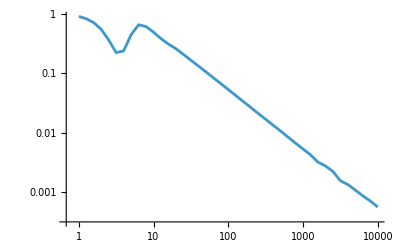

```mathematica
ListLogLogPlot[tabf/.{{x_,y_}->{x,Abs[(y-benchmark)/benchmark]}},Joined->True,GridLines->{{100,500},{0.05,0.01}}]
```